```mathematica
SetDirectory["C:\\Users\\cefit\\source\\repos\\Relaxation Calculation\\Relaxation Calculation"]
```

C:\Users\cefit\source\repos\Relaxation Calculation\Relaxation Calculation

```mathematica
data = Import["relaxation.txt", "Table"]
```

{{1,0.0161667,0.0133724,0.00279433},{1.00833,0.017024,0.0140648,0.00295911},{1.01667,0.0179209,0.0147887,0.00313212},{1.025,0.0188589,0.0155453,0.00331356},{1.03333,0.01984,0.0163359,0.00350403},{1.04167,0.0208656,0.0171619,0.00370367},{1.05,0.0219375,0.0180246,0.00391287},{1.05833,0.0230577,0.0189256,0.0041321},{1.06667,0.0242279,0.0198663,0.00436164},{1.075,0.0254503,0.0208483,0.00460195},{1.08333,0.0267269,0.0218733,0.00485358},{1.09167,0.0280595,0.0229429,0.00511658},{1.1,0.0294507,0.0240589,0.00539173},{1.10833,0.0309025,0.0252231,0.00567937},{1.11667,0.0324173,0.0264374,0.00597985},{1.125,0.0339976,0.0277037,0.00629387},{1.13333,0.0356458,0.0290241,0.00662173},{1.14167,0.0373647,0.0304006,0.00696409},{1.15,0.0391567,0.0318354,0.00732123},{1.15833,0.0410248,0.0333309,0.00769391},{1.16667,0.0429717,0.0348892,0.00808246},{1.175,0.0450006,0.0365129,0.00848768},{1.18333,0.0471144,0.0382044,0.00890997},{1.19167,0.0493163,0.0399663,0.00935},{1.2,0.0516098,0.0418015,0.00980832},{1.20833,0.053998,0.0437125,0.0102855},{1.21667,0.0564849,0.0457025,0.0107824},{1.225,0.0590736,0.0477743,0.0112993},{1.23333,0.0617683,0.049931,0.0118373},{1.24167,0.0645728,0.052176,0.0123968},{1.25,0.067491,0.0545126,0.0129784},{1.25833,0.0705276,0.0569443,0.0135833},{1.26667,0.0736864,0.0594746,0.0142117},{1.275,0.0769721,0.0621074,0.0148647},{1.28333,0.0803894,0.0648465,0.0155429},{1.29167,0.083943,0.0676959,0.0162471},{1.3,0.0876382,0.0706599,0.0169783},{1.30833,0.0914798,0.0737427,0.017737},{1.31667,0.0954733,0.076949,0.0185243},{1.325,0.0996242,0.0802832,0.019341},{1.33333,0.103938,0.0837504,0.0201879},{1.34167,0.108422,0.0873554,0.0210663},{1.35,0.11308,0.0911037,0.0219765},{1.35833,0.11792,0.0950005,0.02292},{1.36667,0.122949,0.0990515,0.0238975},{1.375,0.128173,0.103263,0.0249101},{1.38333,0.133598,0.10764,0.0259587},{1.39167,0.139233,0.112189,0.0270443},{1.4,0.145086,0.116918,0.0281681},{1.40833,0.151163,0.121832,0.0293312},{1.41667,0.157473,0.126939,0.0305347},{1.425,0.164026,0.132246,0.0317797},{1.43333,0.170828,0.137761,0.0330673},{1.44167,0.177889,0.143491,0.0343986},{1.45,0.18522,0.149445,0.035775},{1.45833,0.192829,0.155632,0.0371976},{1.46667,0.200727,0.162059,0.0386676},{1.475,0.208924,0.168737,0.0401866},{1.48333,0.217431,0.175675,0.0417555},{1.49167,0.226259,0.182884,0.0433758},{1.5,0.235421,0.190372,0.0450489},{1.50833,0.244928,0.198151,0.0467762},{1.51667,0.254792,0.206233,0.048559},{1.525,0.265027,0.214629,0.0503987},{1.53333,0.275647,0.22335,0.0522969},{1.54167,0.286665,0.23241,0.0542551},{1.55,0.298097,0.241822,0.0562746},{1.55833,0.309957,0.2516,0.0583572},{1.56667,0.322261,0.261756,0.0605044},{1.575,0.335025,0.272308,0.0627178},{1.58333,0.348267,0.283268,0.0649989},{1.59167,0.362005,0.294655,0.0673495},{1.6,0.376256,0.306484,0.0697715},{1.60833,0.391039,0.318773,0.0722662},{1.61667,0.406375,0.33154,0.0748357},{1.625,0.422285,0.344803,0.0774816},{1.63333,0.438789,0.358583,0.0802058},{1.64167,0.455911,0.3729,0.0830102},{1.65,0.473672,0.387776,0.0858965},{1.65833,0.492099,0.403232,0.0888667},{1.66667,0.511215,0.419292,0.091923},{1.675,0.531047,0.43598,0.095067},{1.68333,0.551622,0.453321,0.098301},{1.69167,0.572969,0.471342,0.101627},{1.7,0.595118,0.490071,0.105047},{1.70833,0.618099,0.509536,0.108563},{1.71667,0.641944,0.529767,0.112177},{1.725,0.666687,0.550795,0.115892},{1.73333,0.692364,0.572654,0.11971},{1.74167,0.71901,0.595377,0.123632},{1.75,0.746663,0.619001,0.127662},{1.75833,0.775364,0.643562,0.131802},{1.76667,0.805154,0.669101,0.136053},{1.775,0.836076,0.695657,0.140419},{1.78333,0.868175,0.723274,0.144902},{1.79167,0.9015,0.751996,0.149504},{1.8,0.936098,0.781871,0.154227},{1.80833,0.972023,0.812947,0.159076},{1.81667,1.00933,0.845276,0.164051},{1.825,1.04807,0.878911,0.169156},{1.83333,1.0883,0.91391,0.174393},{1.84167,1.1301,0.950331,0.179766},{1.85,1.17351,0.988236,0.185276},{1.85833,1.21862,1.02769,0.190926},{1.86667,1.26548,1.06876,0.19672},{1.875,1.31419,1.11152,0.202661},{1.88333,1.3648,1.15605,0.208751},{1.89167,1.41741,1.20242,0.214992},{1.9,1.4721,1.25072,0.22139},{1.90833,1.52897,1.30102,0.227945},{1.91667,1.5881,1.35344,0.234662},{1.925,1.6496,1.40805,0.241543},{1.93333,1.71356,1.46497,0.248591},{1.94167,1.78011,1.5243,0.255811},{1.95,1.84935,1.58614,0.263205},{1.95833,1.92141,1.65063,0.270776},{1.96667,1.99641,1.71788,0.278528},{1.975,2.07449,1.78803,0.286464},{1.98333,2.1558,1.86121,0.294588},{1.99167,2.24047,1.93757,0.302903},{2,2.32868,2.01726,0.311412},{2.00833,2.42057,2.10045,0.32012},{2.01667,2.51634,2.18731,0.329029},{2.025,2.61616,2.27801,0.338144},{2.03333,2.72023,2.37276,0.347468},{2.04167,2.82875,2.47175,0.357005},{2.05,2.94195,2.5752,0.366759},{2.05833,3.06006,2.68333,0.376733},{2.06667,3.18332,2.79638,0.386932},{2.075,3.31198,2.91462,0.39736},{2.08333,3.44633,3.03831,0.40802},{2.09167,3.58665,3.16773,0.418916},{2.1,3.73325,3.3032,0.430053},{2.10833,3.88646,3.44503,0.441435},{2.11667,4.04663,3.59357,0.453065},{2.125,4.21412,3.74918,0.464949},{2.13333,4.38934,3.91225,0.47709},{2.14167,4.57269,4.08319,0.489493},{2.15,4.76462,4.26245,0.502162},{2.15833,4.9656,4.4505,0.515102},{2.16667,5.17614,4.64783,0.528317},{2.175,5.39679,4.85498,0.541812},{2.18333,5.6281,5.07251,0.555591},{2.19167,5.87071,5.30105,0.569658},{2.2,6.12526,5.54124,0.58402},{2.20833,6.39246,5.79378,0.598679},{2.21667,6.67307,6.05943,0.613642},{2.225,6.96788,6.33897,0.628913},{2.23333,7.27777,6.63327,0.644496},{2.24167,7.60366,6.94326,0.660397},{2.25,7.94656,7.26994,0.676622},{2.25833,8.30753,7.61436,0.693174},{2.26667,8.68774,7.97768,0.710058},{2.275,9.08843,8.36115,0.727281},{2.28333,9.51094,8.76609,0.744848},{2.29167,9.95673,9.19397,0.762763},{2.3,10.4274,9.64633,0.781031},{2.30833,10.9245,10.1249,0.79966},{2.31667,11.4501,10.6314,0.818652},{2.325,12.006,11.168,0.838015},{2.33333,12.5944,11.7367,0.857754},{2.34167,13.2178,12.3399,0.877874},{2.35,13.8786,12.9802,0.898381},{2.35833,14.5796,13.6603,0.919281},{2.36667,15.3239,14.3833,0.940579},{2.375,16.1148,15.1525,0.962281},{2.38333,16.956,15.9716,0.984393},{2.39167,17.8513,16.8444,1.00692},{2.4,18.8053,17.7755,1.02987},{2.40833,19.8228,18.7695,1.05325},{2.41667,20.9089,19.8319,1.07706},{2.425,22.0696,20.9683,1.10131},{2.43333,23.3114,22.1854,1.12601},{2.44167,24.6414,23.4902,1.15116},{2.45,26.0674,24.8906,1.17677},{2.45833,27.5984,26.3956,1.20285},{2.46667,29.2442,28.0148,1.2294},{2.475,31.0156,29.7592,1.25642},{2.48333,32.925,31.6411,1.28393},{2.49167,34.9862,33.6742,1.31193},{2.5,37.2144,35.874,1.34043},{2.50833,39.6273,38.2579,1.36943},{2.51667,42.2444,40.8454,1.39895},{2.525,45.088,43.659,1.42898},{2.53333,48.1835,46.724,1.45954},{2.54167,51.5597,50.0691,1.49062},{2.55,55.2498,53.7275,1.52225},{2.55833,59.2916,57.7372,1.55442},{2.56667,63.7288,62.1417,1.58715},{2.575,68.6121,66.9916,1.62044},{2.58333,74,72.3457,1.65429},{2.59167,79.9611,78.2724,1.68872},{2.6,86.5755,84.8518,1.72373},{2.60833,93.9379,92.1786,1.75932},{2.61667,102.16,100.364,1.79552},{2.625,111.375,109.542,1.83232},{2.63333,121.742,119.872,1.86973},{2.64167,133.453,131.546,1.90775},{2.65,146.742,144.796,1.94641},{2.65833,161.894,159.909,1.9857},{2.66667,179.26,177.235,2.02563},{2.675,199.277,197.211,2.06621},{2.68333,222.495,220.387,2.10745},{2.69167,249.609,247.459,2.14935},{2.7,281.512,279.32,2.19193},{2.70833,319.368,317.133,2.23519},{2.71667,364.707,362.428,2.27914},{2.725,419.581,417.257,2.32378},{2.73333,486.787,484.418,2.36913},{2.74167,570.215,567.8,2.4152},{2.75,675.404,672.942,2.46199},{2.75833,810.444,807.935,2.50951},{2.76667,987.534,984.976,2.55777},{2.775,1225.73,1223.13,2.60677},{2.78333,1556.16,1553.51,2.65653},{2.79167,2032.42,2029.71,2.70706},{2.8,2753.18,2750.42,2.75836},{2.80833,3916.51,3913.7,2.81044},{2.81667,5968.93,5966.07,2.86331},{2.825,10098.3,10095.4,2.91698},{2.83333,20398.1,20395.1,2.97145},{2.84167,59644.4,59641.4,3.02675},{2.85,660959,660956,3.08287},{2.85833,389518,389514,3.13982},{2.86667,50996.2,50993,3.19762},{2.875,19002.7,18999.4,3.25628},{2.88333,9842.43,9839.12,3.31579},{2.89167,6005.18,6001.81,3.37617},{2.9,4042.58,4039.14,3.43744},{2.90833,2906.11,2902.61,3.49959},{2.91667,2189.66,2186.1,3.56265},{2.925,1709.14,1705.51,3.62661},{2.93333,1371.28,1367.59,3.69149},{2.94167,1124.74,1120.99,3.7573},{2.95,939.358,935.534,3.82404},{2.95833,796.458,792.566,3.89173},{2.96667,683.992,680.032,3.96038},{2.975,593.898,589.868,4.02999},{2.98333,520.616,516.516,4.10057},{2.99167,460.214,456.042,4.17214},{3,409.843,405.598,4.24471},{3.00833,367.402,363.083,4.31828},{3.01667,331.312,326.919,4.39287},{3.025,300.369,295.901,4.46848},{3.03333,273.641,269.096,4.54512},{3.04167,250.398,245.776,4.62281},{3.05,230.062,225.36,4.70155},{3.05833,212.168,207.387,4.78136},{3.06667,196.343,191.481,4.86224},{3.075,182.281,177.337,4.94421},{3.08333,169.731,164.704,5.02727},{3.09167,158.486,153.375,5.11144},{3.1,148.372,143.175,5.19673},{3.10833,139.244,133.961,5.28314},{3.11667,130.978,125.607,5.37069},{3.125,123.471,118.012,5.45938},{3.13333,116.634,111.085,5.54924},{3.14167,110.391,104.751,5.64026},{3.15,104.676,98.9433,5.73246},{3.15833,99.4315,93.6056,5.82585},{3.16667,94.6089,88.6885,5.92044},{3.175,90.1651,84.1489,6.01624},{3.18333,86.0624,79.9491,6.11326},{3.19167,82.2676,76.056,6.21152},{3.2,78.7516,72.4406,6.31102},{3.20833,75.4887,69.0769,6.41177},{3.21667,72.456,65.9422,6.51379},{3.225,69.6332,63.0162,6.61709},{3.23333,67.0023,60.2806,6.72167},{3.24167,64.547,57.7194,6.82755},{3.25,62.2528,55.318,6.93474},{3.25833,60.1067,53.0635,7.04325},{3.26667,58.097,50.944,7.15309},{3.275,56.2132,48.949,7.26427},{3.28333,54.4457,47.0689,7.37681},{3.29167,52.7858,45.2951,7.49071},{3.3,51.2257,43.6197,7.60599},{3.30833,49.7582,42.0356,7.72265},{3.31667,48.3769,40.5362,7.84072},{3.325,47.0759,39.1157,7.96019},{3.33333,45.8496,37.7685,8.08108},{3.34167,44.6932,36.4897,8.20341},{3.35,43.602,35.2749,8.32719},{3.35833,42.5721,34.1196,8.45241},{3.36667,41.5994,33.0203,8.57911},{3.375,40.6805,31.9732,8.70729},{3.38333,39.8121,30.9751,8.83695},{3.39167,38.9912,30.0231,8.96812},{3.4,38.215,29.1142,9.1008},{3.40833,37.4811,28.2461,9.235},{3.41667,36.7869,27.4162,9.37075},{3.425,36.1303,26.6223,9.50804},{3.43333,35.5093,25.8624,9.64689},{3.44167,34.9219,25.1346,9.78731},{3.45,34.3664,24.4371,9.92932},{3.45833,33.8412,23.7683,10.0729},{3.46667,33.3446,23.1265,10.2181},{3.475,32.8753,22.5103,10.365},{3.48333,32.4319,21.9185,10.5134},{3.49167,32.0132,21.3497,10.6635},{3.5,31.6181,20.8028,10.8153},{3.50833,31.2453,20.2766,10.9687},{3.51667,30.8939,19.7701,11.1238},{3.525,30.563,19.2824,11.2806},{3.53333,30.2516,18.8125,11.4391},{3.54167,29.9589,18.3595,11.5993},{3.55,29.684,17.9228,11.7612},{3.55833,29.4263,17.5014,11.9249},{3.56667,29.1851,17.0947,12.0903},{3.575,28.9596,16.7021,12.2575},{3.58333,28.7493,16.3228,12.4265},{3.59167,28.5535,15.9563,12.5972},{3.6,28.3717,15.6019,12.7698},{3.60833,28.2034,15.2593,12.9441},{3.61667,28.0481,14.9278,13.1203},{3.625,27.9054,14.607,13.2983},{3.63333,27.7747,14.2965,13.4782},{3.64167,27.6556,13.9957,13.6599},{3.65,27.5478,13.7044,13.8435},{3.65833,27.451,13.422,14.029},{3.66667,27.3646,13.1483,14.2163},{3.675,27.2884,12.8828,14.4056},{3.68333,27.2222,12.6253,14.5968},{3.69167,27.1654,12.3755,14.7899},{3.7,27.118,12.133,14.985},{3.70833,27.0796,11.8976,15.182},{3.71667,27.05,11.6689,15.381},{3.725,27.0288,11.4468,15.582},{3.73333,27.0159,11.231,15.785},{3.74167,27.0111,11.0212,15.9899},{3.75,27.0141,10.8172,16.1969},{3.75833,27.0248,10.6189,16.4059},{3.76667,27.0429,10.4259,16.617},{3.775,27.0683,10.2382,16.8301},{3.78333,27.1007,10.0555,17.0453},{3.79167,27.1401,9.87761,17.2625},{3.8,27.1863,9.70442,17.4819},{3.80833,27.2391,9.53575,17.7033},{3.81667,27.2983,9.37143,17.9269},{3.825,27.3639,9.21133,18.1526},{3.83333,27.4357,9.0553,18.3804},{3.84167,27.5136,8.9032,18.6104},{3.85,27.5974,8.7549,18.8425},{3.85833,27.6871,8.61027,19.0768},{3.86667,27.7825,8.4692,19.3133},{3.875,27.8836,8.33156,19.552},{3.88333,27.9902,8.19726,19.7929},{3.89167,28.1022,8.06617,20.036},{3.9,28.2196,7.93821,20.2814},{3.90833,28.3423,7.81326,20.529},{3.91667,28.4701,7.69125,20.7789},{3.925,28.6031,7.57207,21.031},{3.93333,28.7411,7.45563,21.2854},{3.94167,28.884,7.34187,21.5421},{3.95,29.0318,7.23068,21.8012},{3.95833,29.1845,7.12201,22.0625},{3.96667,29.3419,7.01576,22.3262},{3.975,29.5041,6.91188,22.5922},{3.98333,29.6708,6.81029,22.8606},{3.99167,29.8422,6.71091,23.1313},{4,30.0181,6.6137,23.4044},{4.00833,30.1985,6.51859,23.6799},{4.01667,30.3833,6.42551,23.9578},{4.025,30.5725,6.33441,24.2381},{4.03333,30.7661,6.24524,24.5209},{4.04167,30.964,6.15794,24.806},{4.05,31.1661,6.07245,25.0937},{4.05833,31.3725,5.98873,25.3838},{4.06667,31.5831,5.90673,25.6763},{4.075,31.7978,5.82641,25.9714},{4.08333,32.0166,5.74771,26.2689},{4.09167,32.2395,5.67059,26.5689},{4.1,32.4665,5.59502,26.8715},{4.10833,32.6975,5.52095,27.1766},{4.11667,32.9326,5.44833,27.4842},{4.125,33.1716,5.37715,27.7944},{4.13333,33.4145,5.30734,28.1072},{4.14167,33.6614,5.23889,28.4225},{4.15,33.9122,5.17176,28.7404},{4.15833,34.1668,5.1059,29.0609},{4.16667,34.4253,5.0413,29.384},{4.175,34.6877,4.97791,29.7098},{4.18333,34.9538,4.91572,30.0381},{4.19167,35.2238,4.85468,30.3691},{4.2,35.4976,4.79477,30.7028},{4.20833,35.7751,4.73596,31.0391},{4.21667,36.0564,4.67823,31.3781},{4.225,36.3414,4.62155,31.7198},{4.23333,36.6301,4.56589,32.0642},{4.24167,36.9225,4.51123,32.4113},{4.25,37.2187,4.45755,32.7611},{4.25833,37.5185,4.40481,33.1137},{4.26667,37.822,4.35301,33.469},{4.275,38.1291,4.30212,33.827},{4.28333,38.4399,4.25212,34.1878},{4.29167,38.7544,4.20298,34.5514},{4.3,39.0725,4.15469,34.9178},{4.30833,39.3941,4.10722,35.2869},{4.31667,39.7195,4.06057,35.6589},{4.325,40.0484,4.0147,36.0337},{4.33333,40.3809,3.96961,36.4113},{4.34167,40.717,3.92528,36.7917},{4.35,41.0567,3.88168,37.175},{4.35833,41.3999,3.8388,37.5611},{4.36667,41.7468,3.79663,37.9501},{4.375,42.0972,3.75516,38.342},{4.38333,42.4512,3.71435,38.7368},{4.39167,42.8087,3.67421,39.1345},{4.4,43.1698,3.63472,39.5351},{4.40833,43.5344,3.59586,39.9386},{4.41667,43.9026,3.55762,40.345},{4.425,44.2744,3.51999,40.7544},{4.43333,44.6496,3.48295,41.1667},{4.44167,45.0284,3.44649,41.5819},{4.45,45.4108,3.4106,42.0002},{4.45833,45.7967,3.37527,42.4214},{4.46667,46.1861,3.34049,42.8456},{4.475,46.579,3.30624,43.2728},{4.48333,46.9755,3.27251,43.703},{4.49167,47.3755,3.2393,44.1362},{4.5,47.779,3.20659,44.5724},{4.50833,48.1861,3.17438,45.0117},{4.51667,48.5966,3.14264,45.454},{4.525,49.0108,3.11138,45.8994},{4.53333,49.4284,3.08059,46.3478},{4.54167,49.8495,3.05025,46.7993},{4.55,50.2742,3.02035,47.2539},{4.55833,50.7024,2.9909,47.7115},{4.56667,51.1341,2.96187,48.1723},{4.575,51.5694,2.93326,48.6361},{4.58333,52.0082,2.90506,49.1031},{4.59167,52.4505,2.87727,49.5732},{4.6,52.8963,2.84988,50.0464},{4.60833,53.3457,2.82288,50.5228},{4.61667,53.7986,2.79625,51.0023},{4.625,54.255,2.77001,51.485},{4.63333,54.7149,2.74413,51.9708},{4.64167,55.1784,2.71861,52.4598},{4.65,55.6454,2.69344,52.952},{4.65833,56.116,2.66863,53.4474},{4.66667,56.5901,2.64415,53.9459},{4.675,57.0677,2.62001,54.4477},{4.68333,57.5489,2.5962,54.9527},{4.69167,58.0336,2.57271,55.4609},{4.7,58.5219,2.54954,55.9724},{4.70833,59.0137,2.52668,56.4871},{4.71667,59.5091,2.50413,57.005},{4.725,60.008,2.48188,57.5261},{4.73333,60.5105,2.45992,58.0506},{4.74167,61.0165,2.43825,58.5783},{4.75,61.5261,2.41687,59.1093},{4.75833,62.0393,2.39577,59.6435},{4.76667,62.556,2.37494,60.181},{4.775,63.0763,2.35439,60.7219},{4.78333,63.6001,2.3341,61.266},{4.79167,64.1275,2.31407,61.8135},{4.8,64.6585,2.29429,62.3642},{4.80833,65.1931,2.27477,62.9183},{4.81667,65.7312,2.2555,63.4757},{4.825,66.273,2.23647,64.0365},{4.83333,66.8183,2.21769,64.6006},{4.84167,67.3672,2.19913,65.168},{4.85,67.9196,2.18081,65.7388},{4.85833,68.4757,2.16272,66.313},{4.86667,69.0354,2.14485,66.8905},{4.875,69.5986,2.1272,67.4714},{4.88333,70.1655,2.10977,68.0557},{4.89167,70.7359,2.09255,68.6434},{4.9,71.31,2.07554,69.2344},{4.90833,71.8876,2.05874,69.8289},{4.91667,72.4689,2.04214,70.4267},{4.925,73.0538,2.02575,71.028},{4.93333,73.6423,2.00955,71.6327},{4.94167,74.2344,1.99354,72.2408},{4.95,74.8301,1.97772,72.8524},{4.95833,75.4294,1.96209,73.4673},{4.96667,76.0324,1.94664,74.0857},{4.975,76.6389,1.93138,74.7076},{4.98333,77.2491,1.9163,75.3328},{4.99167,77.863,1.90139,75.9616},{5,78.4804,1.88665,76.5938},{5.00833,79.1015,1.87209,77.2294},{5.01667,79.7263,1.85769,77.8686},{5.025,80.3546,1.84346,78.5112},{5.03333,80.9866,1.82939,79.1572},{5.04167,81.6223,1.81548,79.8068},{5.05,82.2616,1.80173,80.4598},{5.05833,82.9045,1.78814,81.1164},{5.06667,83.5511,1.7747,81.7764},{5.075,84.2013,1.7614,82.4399},{5.08333,84.8552,1.74826,83.1069},{5.09167,85.5127,1.73527,83.7774},{5.1,86.1739,1.72242,84.4515},{5.10833,86.8387,1.70971,85.129},{5.11667,87.5072,1.69714,85.8101},{5.125,88.1794,1.68471,86.4947},{5.13333,88.8552,1.67242,87.1828},{5.14167,89.5347,1.66026,87.8744},{5.15,90.2178,1.64823,88.5696},{5.15833,90.9046,1.63633,89.2683},{5.16667,91.5951,1.62456,89.9705},{5.175,92.2892,1.61292,90.6763},{5.18333,92.987,1.6014,91.3856},{5.19167,93.6885,1.59001,92.0985},{5.2,94.3936,1.57873,92.8149},{5.20833,95.1024,1.56758,93.5348},{5.21667,95.8149,1.55654,94.2584},{5.225,96.5311,1.54562,94.9854},{5.23333,97.2509,1.53481,95.7161},{5.24167,97.9744,1.52412,96.4503},{5.25,98.7016,1.51354,97.188},{5.25833,99.4324,1.50307,97.9294},{5.26667,100.167,1.4927,98.6743},{5.275,100.905,1.48245,99.4227},{5.28333,101.647,1.4723,100.175},{5.29167,102.393,1.46225,100.93},{5.3,103.142,1.4523,101.69},{5.30833,103.895,1.44246,102.452},{5.31667,104.651,1.43272,103.219},{5.325,105.412,1.42307,103.989},{5.33333,106.176,1.41352,104.762},{5.34167,106.943,1.40407,105.539},{5.35,107.715,1.39471,106.32},{5.35833,108.49,1.38544,107.104},{5.36667,109.268,1.37627,107.892},{5.375,110.051,1.36719,108.684},{5.38333,110.837,1.3582,109.479},{5.39167,111.627,1.34929,110.277},{5.4,112.42,1.34048,111.079},{5.40833,113.217,1.33174,111.885},{5.41667,114.018,1.3231,112.695},{5.425,114.822,1.31454,113.508},{5.43333,115.63,1.30606,114.324},{5.44167,116.442,1.29766,115.144},{5.45,117.258,1.28934,115.968},{5.45833,118.077,1.28111,116.796},{5.46667,118.9,1.27295,117.627},{5.475,119.726,1.26487,118.461},{5.48333,120.556,1.25686,119.299},{5.49167,121.39,1.24894,120.141},{5.5,122.228,1.24108,120.986},{5.50833,123.069,1.2333,121.835},{5.51667,123.914,1.2256,122.688},{5.525,124.762,1.21796,123.544},{5.53333,125.614,1.2104,124.404},{5.54167,126.47,1.20291,125.267},{5.55,127.329,1.19548,126.134},{5.55833,128.193,1.18813,127.004},{5.56667,129.059,1.18084,127.879},{5.575,129.93,1.17362,128.756},{5.58333,130.804,1.16646,129.637},{5.59167,131.682,1.15937,130.522},{5.6,132.563,1.15235,131.411},{5.60833,133.448,1.14539,132.303},{5.61667,134.337,1.13849,133.198},{5.625,135.229,1.13165,134.097},{5.63333,136.125,1.12488,135},{5.64167,137.025,1.11816,135.907},{5.65,137.928,1.11151,136.816},{5.65833,138.835,1.10491,137.73},{5.66667,139.745,1.09838,138.647},{5.675,140.659,1.0919,139.568},{5.68333,141.577,1.08548,140.492},{5.69167,142.499,1.07911,141.419},{5.7,143.423,1.0728,142.351},{5.70833,144.352,1.06655,143.286},{5.71667,145.284,1.06035,144.224},{5.725,146.22,1.0542,145.166},{5.73333,147.16,1.04811,146.111},{5.74167,148.103,1.04207,147.06},{5.75,149.049,1.03608,148.013},{5.75833,149.999,1.03015,148.969},{5.76667,150.953,1.02426,149.929},{5.775,151.911,1.01843,150.892},{5.78333,152.872,1.01264,151.859},{5.79167,153.836,1.0069,152.829},{5.8,154.804,1.00122,153.803},{5.80833,155.776,0.995577,154.78},{5.81667,156.751,0.989985,155.761},{5.825,157.73,0.98444,156.746},{5.83333,158.712,0.978942,157.733},{5.84167,159.698,0.973489,158.725},{5.85,160.688,0.968082,159.72},{5.85833,161.681,0.962719,160.718},{5.86667,162.677,0.957401,161.72},{5.875,163.678,0.952127,162.725},{5.88333,164.681,0.946897,163.734},{5.89167,165.688,0.941709,164.747},{5.9,166.699,0.936564,165.763},{5.90833,167.713,0.931461,166.782},{5.91667,168.731,0.9264,167.805},{5.925,169.752,0.92138,168.831},{5.93333,170.777,0.9164,169.861},{5.94167,171.805,0.911461,170.894},{5.95,172.837,0.906562,171.931},{5.95833,173.872,0.901702,172.971},{5.96667,174.911,0.89688,174.014},{5.975,175.953,0.892098,175.061},{5.98333,176.999,0.887354,176.112},{5.99167,178.048,0.882647,177.166},{6,179.101,0.877978,178.223},{6.00833,180.157,0.873345,179.284},{6.01667,181.217,0.86875,180.348},{6.025,182.28,0.86419,181.415},{6.03333,183.346,0.859666,182.486},{6.04167,184.416,0.855178,183.561},{6.05,185.489,0.850725,184.638},{6.05833,186.566,0.846306,185.72},{6.06667,187.646,0.841922,186.804},{6.075,188.73,0.837572,187.892},{6.08333,189.817,0.833255,188.983},{6.09167,190.907,0.828972,190.078},{6.1,192.001,0.824721,191.176},{6.10833,193.098,0.820503,192.277},{6.11667,194.198,0.816318,193.382},{6.125,195.302,0.812164,194.49},{6.13333,196.41,0.808042,195.602},{6.14167,197.52,0.803952,196.716},{6.15,198.634,0.799892,197.834},{6.15833,199.752,0.795863,198.956},{6.16667,200.872,0.791865,200.08},{6.175,201.996,0.787896,201.208},{6.18333,203.124,0.783957,202.34},{6.19167,204.254,0.780048,203.474},{6.2,205.388,0.776168,204.612},{6.20833,206.526,0.772316,205.753},{6.21667,207.666,0.768493,206.898},{6.225,208.81,0.764699,208.045},{6.23333,209.957,0.760933,209.196},{6.24167,211.108,0.757194,210.351},{6.25,212.262,0.753483,211.508},{6.25833,213.419,0.749799,212.669},{6.26667,214.579,0.746142,213.833},{6.275,215.742,0.742512,215},{6.28333,216.909,0.738908,216.17},{6.29167,218.079,0.73533,217.344},{6.3,219.252,0.731779,218.521},{6.30833,220.429,0.728253,219.701},{6.31667,221.609,0.724752,220.884},{6.325,222.792,0.721276,222.07},{6.33333,223.978,0.717826,223.26},{6.34167,225.167,0.7144,224.453},{6.35,226.359,0.710999,225.648},{6.35833,227.555,0.707622,226.847},{6.36667,228.754,0.704268,228.05},{6.375,229.956,0.700939,229.255},{6.38333,231.161,0.697633,230.463},{6.39167,232.369,0.694351,231.675},{6.4,233.581,0.691092,232.89},{6.40833,234.795,0.687855,234.107},{6.41667,236.013,0.684641,235.328},{6.425,237.234,0.68145,236.552},{6.43333,238.458,0.678281,237.779},{6.44167,239.685,0.675134,239.01},{6.45,240.915,0.672009,240.243},{6.45833,242.148,0.668905,241.479},{6.46667,243.384,0.665823,242.718},{6.475,244.623,0.662763,243.961},{6.48333,245.866,0.659723,245.206},{6.49167,247.111,0.656704,246.455},{6.5,248.36,0.653706,247.706},{6.50833,249.611,0.650728,248.96},{6.51667,250.866,0.647771,250.218},{6.525,252.123,0.644833,251.478},{6.53333,253.384,0.641916,252.742},{6.54167,254.647,0.639018,254.008},{6.55,255.914,0.63614,255.278},{6.55833,257.183,0.633282,256.55},{6.56667,258.456,0.630442,257.825},{6.575,259.731,0.627622,259.104},{6.58333,261.01,0.624821,260.385},{6.59167,262.291,0.622038,261.669},{6.6,263.575,0.619274,262.956},{6.60833,264.862,0.616528,264.246},{6.61667,266.152,0.6138,265.539},{6.625,267.445,0.611091,266.834},{6.63333,268.741,0.608399,268.133},{6.64167,270.04,0.605725,269.434},{6.65,271.342,0.603069,270.739},{6.65833,272.646,0.60043,272.046},{6.66667,273.954,0.597808,273.356},{6.675,275.264,0.595204,274.669},{6.68333,276.577,0.592616,275.985},{6.69167,277.893,0.590046,277.303},{6.7,279.212,0.587492,278.625},{6.70833,280.534,0.584954,279.949},{6.71667,281.858,0.582433,281.276},{6.725,283.185,0.579929,282.605},{6.73333,284.515,0.57744,283.938},{6.74167,285.848,0.574968,285.273},{6.75,287.184,0.572511,286.611},{6.75833,288.522,0.57007,287.952},{6.76667,289.863,0.567644,289.295},{6.775,291.207,0.565234,290.642},{6.78333,292.553,0.56284,291.991},{6.79167,293.903,0.56046,293.342},{6.8,295.255,0.558095,294.697},{6.80833,296.609,0.555746,296.054},{6.81667,297.967,0.553411,297.413},{6.825,299.327,0.551091,298.776},{6.83333,300.69,0.548786,300.141},{6.84167,302.055,0.546495,301.509},{6.85,303.423,0.544218,302.879},{6.85833,304.794,0.541955,304.252},{6.86667,306.167,0.539707,305.628},{6.875,307.543,0.537472,307.006},{6.88333,308.922,0.535252,308.387},{6.89167,310.303,0.533045,309.77},{6.9,311.687,0.530852,311.156},{6.90833,313.074,0.528672,312.545},{6.91667,314.463,0.526505,313.936},{6.925,315.854,0.524352,315.33},{6.93333,317.248,0.522212,316.726},{6.94167,318.645,0.520085,318.125},{6.95,320.044,0.517972,319.526},{6.95833,321.446,0.515871,320.93},{6.96667,322.85,0.513782,322.337},{6.975,324.257,0.511707,323.745},{6.98333,325.667,0.509644,325.157},{6.99167,327.078,0.507593,326.571},{7,328.493,0.505555,327.987},{7.00833,329.909,0.503529,329.406},{7.01667,331.329,0.501515,330.827},{7.025,332.75,0.499513,332.251},{7.03333,334.174,0.497523,333.677},{7.04167,335.601,0.495545,335.105},{7.05,337.03,0.493579,336.536},{7.05833,338.461,0.491625,337.97},{7.06667,339.895,0.489682,339.406},{7.075,341.331,0.48775,340.844},{7.08333,342.77,0.48583,342.284},{7.09167,344.211,0.483922,343.727},{7.1,345.654,0.482024,345.172},{7.10833,347.1,0.480138,346.62},{7.11667,348.548,0.478262,348.07},{7.125,349.999,0.476398,349.522},{7.13333,351.451,0.474545,350.977},{7.14167,352.906,0.472702,352.434},{7.15,354.364,0.47087,353.893},{7.15833,355.823,0.469049,355.354},{7.16667,357.285,0.467238,356.818},{7.175,358.749,0.465438,358.284},{7.18333,360.216,0.463648,359.752},{7.19167,361.685,0.461868,361.223},{7.2,363.155,0.460099,362.695},{7.20833,364.629,0.45834,364.17},{7.21667,366.104,0.45659,365.648},{7.225,367.582,0.454851,367.127},{7.23333,369.062,0.453122,368.608},{7.24167,370.544,0.451403,370.092},{7.25,372.028,0.449693,371.578},{7.25833,373.514,0.447993,373.066},{7.26667,375.003,0.446303,374.557},{7.275,376.494,0.444622,376.049},{7.28333,377.987,0.442951,377.544},{7.29167,379.482,0.441289,379.04},{7.3,380.979,0.439636,380.539},{7.30833,382.478,0.437993,382.04},{7.31667,383.979,0.436359,383.543},{7.325,385.483,0.434734,385.048},{7.33333,386.989,0.433118,386.555},{7.34167,388.496,0.431511,388.065},{7.35,390.006,0.429913,389.576},{7.35833,391.518,0.428324,391.089},{7.36667,393.032,0.426743,392.605},{7.375,394.547,0.425172,394.122},{7.38333,396.065,0.423609,395.642},{7.39167,397.585,0.422055,397.163},{7.4,399.107,0.420509,398.687},{7.40833,400.631,0.418971,400.212},{7.41667,402.157,0.417443,401.74},{7.425,403.685,0.415922,403.269},{7.43333,405.215,0.41441,404.8},{7.44167,406.747,0.412906,406.334},{7.45,408.281,0.41141,407.869},{7.45833,409.816,0.409922,409.406},{7.46667,411.354,0.408442,410.946},{7.475,412.894,0.406971,412.487},{7.48333,414.435,0.405507,414.03},{7.49167,415.978,0.404051,415.574},{7.5,417.524,0.402603,417.121},{7.50833,419.071,0.401163,418.67},{7.51667,420.62,0.39973,420.22},{7.525,422.171,0.398305,421.773},{7.53333,423.724,0.396888,423.327},{7.54167,425.278,0.395478,424.883},{7.55,426.835,0.394076,426.441},{7.55833,428.393,0.392681,428},{7.56667,429.953,0.391294,429.562},{7.575,431.515,0.389914,431.125},{7.58333,433.079,0.388541,432.69},{7.59167,434.644,0.387176,434.257},{7.6,436.212,0.385817,435.826},{7.60833,437.781,0.384466,437.396},{7.61667,439.352,0.383122,438.968},{7.625,440.924,0.381785,440.542},{7.63333,442.498,0.380455,442.118},{7.64167,444.074,0.379132,443.695},{7.65,445.652,0.377815,445.274},{7.65833,447.232,0.376506,446.855},{7.66667,448.813,0.375203,448.438},{7.675,450.396,0.373907,450.022},{7.68333,451.98,0.372618,451.608},{7.69167,453.566,0.371336,453.195},{7.7,455.154,0.37006,454.784},{7.70833,456.744,0.36879,456.375},{7.71667,458.335,0.367527,457.967},{7.725,459.928,0.366271,459.561},{7.73333,461.522,0.365021,461.157},{7.74167,463.118,0.363778,462.754},{7.75,464.716,0.36254,464.353},{7.75833,466.315,0.36131,465.954},{7.76667,467.916,0.360085,467.556},{7.775,469.518,0.358866,469.16},{7.78333,471.122,0.357654,470.765},{7.79167,472.728,0.356448,472.372},{7.8,474.335,0.355248,473.98},{7.80833,475.944,0.354054,475.59},{7.81667,477.554,0.352866,477.201},{7.825,479.166,0.351684,478.814},{7.83333,480.779,0.350508,480.428},{7.84167,482.394,0.349338,482.044},{7.85,484.01,0.348174,483.662},{7.85833,485.628,0.347015,485.281},{7.86667,487.247,0.345862,486.901},{7.875,488.867,0.344715,488.523},{7.88333,490.49,0.343574,490.146},{7.89167,492.113,0.342438,491.771},{7.9,493.738,0.341308,493.397},{7.90833,495.365,0.340184,495.024},{7.91667,496.992,0.339065,496.653},{7.925,498.622,0.337952,498.284},{7.93333,500.252,0.336844,499.916},{7.94167,501.885,0.335741,501.549},{7.95,503.518,0.334644,503.183},{7.95833,505.153,0.333552,504.819},{7.96667,506.789,0.332466,506.457},{7.975,508.427,0.331385,508.095},{7.98333,510.066,0.330309,509.735},{7.99167,511.706,0.329239,511.377},{8,513.348,0.328173,513.019},{8.00833,514.991,0.327113,514.663},{8.01667,516.635,0.326058,516.309},{8.025,518.28,0.325008,517.955},{8.03333,519.927,0.323963,519.603},{8.04167,521.575,0.322923,521.252},{8.05,523.225,0.321888,522.903},{8.05833,524.876,0.320858,524.555},{8.06667,526.528,0.319833,526.208},{8.075,528.181,0.318813,527.862},{8.08333,529.835,0.317798,529.517},{8.09167,531.491,0.316787,531.174},{8.1,533.148,0.315782,532.832},{8.10833,534.806,0.314781,534.491},{8.11667,536.465,0.313785,536.152},{8.125,538.126,0.312794,537.813},{8.13333,539.788,0.311807,539.476},{8.14167,541.451,0.310825,541.14},{8.15,543.115,0.309848,542.805},{8.15833,544.78,0.308875,544.471},{8.16667,546.447,0.307907,546.139},{8.175,548.114,0.306943,547.807},{8.18333,549.783,0.305984,549.477},{8.19167,551.453,0.30503,551.148},{8.2,553.124,0.30408,552.82},{8.20833,554.796,0.303134,554.493},{8.21667,556.469,0.302193,556.167},{8.225,558.144,0.301256,557.842},{8.23333,559.819,0.300323,559.519},{8.24167,561.496,0.299395,561.196},{8.25,563.173,0.298471,562.875},{8.25833,564.852,0.297551,564.554},{8.26667,566.531,0.296636,566.235},{8.275,568.212,0.295724,567.916},{8.28333,569.894,0.294817,569.599},{8.29167,571.577,0.293914,571.283},{8.3,573.261,0.293016,572.968},{8.30833,574.946,0.292121,574.653},{8.31667,576.631,0.291231,576.34},{8.325,578.318,0.290344,578.028},{8.33333,580.006,0.289462,579.717},{8.34167,581.695,0.288583,581.406},{8.35,583.385,0.287709,583.097},{8.35833,585.076,0.286838,584.789},{8.36667,586.767,0.285972,586.481},{8.375,588.46,0.285109,588.175},{8.38333,590.154,0.284251,589.869},{8.39167,591.848,0.283396,591.565},{8.4,593.544,0.282545,593.261},{8.40833,595.24,0.281698,594.958},{8.41667,596.937,0.280855,596.657},{8.425,598.636,0.280015,598.356},{8.43333,600.335,0.279179,600.056},{8.44167,602.035,0.278347,601.756},{8.45,603.736,0.277519,603.458},{8.45833,605.437,0.276694,605.161},{8.46667,607.14,0.275873,606.864},{8.475,608.843,0.275056,608.568},{8.48333,610.548,0.274242,610.273},{8.49167,612.253,0.273432,611.979},{8.5,613.959,0.272626,613.686},{8.50833,615.665,0.271823,615.393},{8.51667,617.373,0.271023,617.102},{8.525,619.081,0.270227,618.811},{8.53333,620.79,0.269435,620.521},{8.54167,622.5,0.268646,622.232},{8.55,624.211,0.267861,623.943},{8.55833,625.922,0.267079,625.655},{8.56667,627.635,0.2663,627.368},{8.575,629.348,0.265525,629.082},{8.58333,631.061,0.264753,630.797},{8.59167,632.776,0.263985,632.512},{8.6,634.491,0.26322,634.228},{8.60833,636.207,0.262458,635.945},{8.61667,637.924,0.261699,637.662},{8.625,639.641,0.260944,639.38},{8.63333,641.359,0.260192,641.099},{8.64167,643.078,0.259443,642.818},{8.65,644.797,0.258698,644.538},{8.65833,646.517,0.257956,646.259},{8.66667,648.238,0.257217,647.981},{8.675,649.959,0.256481,649.703},{8.68333,651.681,0.255748,651.426},{8.69167,653.404,0.255019,653.149},{8.7,655.127,0.254292,654.873},{8.70833,656.851,0.253569,656.598},{8.71667,658.576,0.252848,658.323},{8.725,660.301,0.252131,660.049},{8.73333,662.027,0.251417,661.775},{8.74167,663.753,0.250706,663.502},{8.75,665.48,0.249998,665.23},{8.75833,667.208,0.249293,666.958},{8.76667,668.936,0.24859,668.687},{8.775,670.664,0.247891,670.416},{8.78333,672.394,0.247195,672.146},{8.79167,674.123,0.246502,673.877},{8.8,675.854,0.245811,675.608},{8.80833,677.584,0.245124,677.339},{8.81667,679.316,0.244439,679.071},{8.825,681.048,0.243757,680.804},{8.83333,682.78,0.243078,682.537},{8.84167,684.513,0.242402,684.27},{8.85,686.246,0.241729,686.004},{8.85833,687.98,0.241058,687.739},{8.86667,689.714,0.240391,689.474},{8.875,691.449,0.239726,691.209},{8.88333,693.184,0.239064,692.945},{8.89167,694.92,0.238404,694.681},{8.9,696.656,0.237748,696.418},{8.90833,698.392,0.237094,698.155},{8.91667,700.129,0.236442,699.893},{8.925,701.867,0.235794,701.631},{8.93333,703.604,0.235148,703.369},{8.94167,705.343,0.234504,705.108},{8.95,707.081,0.233864,706.847},{8.95833,708.82,0.233226,708.587},{8.96667,710.56,0.23259,710.327},{8.975,712.299,0.231957,712.067},{8.98333,714.039,0.231327,713.808},{8.99167,715.78,0.230699,715.549},{9,717.52,0.230074,717.29},{9.00833,719.262,0.229452,719.032},{9.01667,721.003,0.228832,720.774},{9.025,722.745,0.228214,722.517},{9.03333,724.487,0.227599,724.259},{9.04167,726.229,0.226986,726.002},{9.05,727.972,0.226376,727.745},{9.05833,729.715,0.225769,729.489},{9.06667,731.458,0.225163,731.233},{9.075,733.202,0.224561,732.977},{9.08333,734.945,0.22396,734.721},{9.09167,736.689,0.223362,736.466},{9.1,738.434,0.222767,738.211},{9.10833,740.178,0.222173,739.956},{9.11667,741.923,0.221583,741.701},{9.125,743.668,0.220994,743.447},{9.13333,745.413,0.220408,745.193},{9.14167,747.159,0.219824,746.939},{9.15,748.904,0.219243,748.685},{9.15833,750.65,0.218664,750.431},{9.16667,752.396,0.218087,752.178},{9.175,754.142,0.217512,753.925},{9.18333,755.888,0.21694,755.672},{9.19167,757.635,0.21637,757.419},{9.2,759.382,0.215802,759.166},{9.20833,761.128,0.215236,760.913},{9.21667,762.875,0.214673,762.661},{9.225,764.622,0.214111,764.408},{9.23333,766.37,0.213553,766.156},{9.24167,768.117,0.212996,767.904},{9.25,769.864,0.212441,769.652},{9.25833,771.612,0.211889,771.4},{9.26667,773.359,0.211338,773.148},{9.275,775.107,0.21079,774.896},{9.28333,776.855,0.210244,776.644},{9.29167,778.602,0.2097,778.393},{9.3,780.35,0.209158,780.141},{9.30833,782.098,0.208619,781.889},{9.31667,783.846,0.208081,783.638},{9.325,785.594,0.207546,785.386},{9.33333,787.342,0.207012,787.135},{9.34167,789.09,0.20648,788.883},{9.35,790.838,0.205951,790.632},{9.35833,792.586,0.205424,792.38},{9.36667,794.334,0.204898,794.129},{9.375,796.082,0.204375,795.877},{9.38333,797.83,0.203854,797.626},{9.39167,799.577,0.203334,799.374},{9.4,801.325,0.202817,801.122},{9.40833,803.073,0.202302,802.871},{9.41667,804.821,0.201788,804.619},{9.425,806.568,0.201277,806.367},{9.43333,808.316,0.200767,808.115},{9.44167,810.063,0.20026,809.863},{9.45,811.811,0.199754,811.611},{9.45833,813.558,0.19925,813.359},{9.46667,815.305,0.198748,815.106},{9.475,817.052,0.198249,816.854},{9.48333,818.799,0.197751,818.601},{9.49167,820.546,0.197254,820.348},{9.5,822.292,0.19676,822.096},{9.50833,824.039,0.196267,823.842},{9.51667,825.785,0.195777,825.589},{9.525,827.531,0.195288,827.336},{9.53333,829.277,0.194801,829.082},{9.54167,831.023,0.194316,830.828},{9.55,832.768,0.193833,832.574},{9.55833,834.514,0.193351,834.32},{9.56667,836.259,0.192871,836.066},{9.575,838.003,0.192393,837.811},{9.58333,839.748,0.191917,839.556},{9.59167,841.492,0.191443,841.301},{9.6,843.237,0.19097,843.046},{9.60833,844.98,0.190499,844.79},{9.61667,846.724,0.19003,846.534},{9.625,848.467,0.189563,848.278},{9.63333,850.21,0.189097,850.021},{9.64167,851.953,0.188633,851.764},{9.65,853.695,0.188171,853.507},{9.65833,855.438,0.18771,855.25},{9.66667,857.179,0.187251,856.992},{9.675,858.921,0.186794,858.734},{9.68333,860.662,0.186338,860.476},{9.69167,862.403,0.185884,862.217},{9.7,864.143,0.185432,863.958},{9.70833,865.883,0.184982,865.698},{9.71667,867.623,0.184533,867.438},{9.725,869.362,0.184085,869.178},{9.73333,871.101,0.18364,870.917},{9.74167,872.839,0.183196,872.656},{9.75,874.577,0.182753,874.394},{9.75833,876.315,0.182312,876.132},{9.76667,878.052,0.181873,877.87},{9.775,879.789,0.181435,879.607},{9.78333,881.525,0.180999,881.344},{9.79167,883.261,0.180565,883.08},{9.8,884.996,0.180132,884.816},{9.80833,886.731,0.1797,886.551},{9.81667,888.465,0.17927,888.286},{9.825,890.199,0.178842,890.02},{9.83333,891.932,0.178415,891.754},{9.84167,893.665,0.17799,893.487},{9.85,895.398,0.177566,895.22},{9.85833,897.129,0.177144,896.952},{9.86667,898.861,0.176723,898.684},{9.875,900.591,0.176304,900.415},{9.88333,902.321,0.175886,902.146},{9.89167,904.051,0.17547,903.875},{9.9,905.78,0.175055,905.605},{9.90833,907.508,0.174642,907.334},{9.91667,909.236,0.17423,909.062},{9.925,910.963,0.17382,910.789},{9.93333,912.69,0.173411,912.516},{9.94167,914.416,0.173003,914.243},{9.95,916.141,0.172597,915.968},{9.95833,917.865,0.172192,917.693},{9.96667,919.589,0.171789,919.417},{9.975,921.313,0.171387,921.141},{9.98333,923.035,0.170987,922.864},{9.99167,924.757,0.170588,924.586},{10,926.478,0.17019,926.308}}

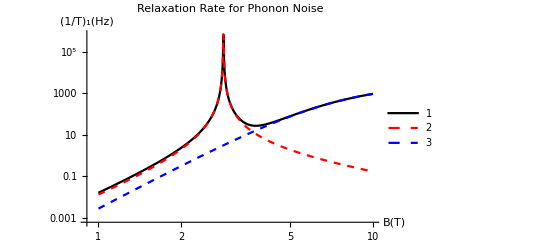

```mathematica
ListLogLogPlot[Transpose[Thread[{First[#],Rest[#]}]&/@data] ,Joined->True, AxesLabel->{"B(T)", "\!\(\*SubscriptBox[\(1/T\), \(1\)]\)(Hz)"},PlotLegends->Automatic,PlotStyle->{{Solid, Black}, {Dashed, Red}, {Dashed, Blue}} ,PlotLabel->"Relaxation Rate for Phonon Noise"]
```